# Absorption Imaging in High Magnetic Field for Rb87 at D2 line

Here we show the zeeman spliting for D2 line(Ground state and Excited state) of Rb87, then calculate the dipole matrix of it under high magnetic field. By analyze dipole matrix, we give the possible way for HF-imaging of different spin states of Rb87.

Load the package. Here we use the AtomicDensityMatrix tool for getting atomic information(such as Rb87 and Na23)

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<AtomicDensityMatrix`
```

```mathematica
<<Units`
```

Set options for DensityMatrix and a plotting function.

```mathematica
SetOptions[DensityMatrix,TimeDependence->False,ComplexExpandVariables->Subscript];
```

```mathematica
SetOptions[ListLinePlot,PlotRange->All,ImageSize->Medium,Frame->True];
```

Choose a transition. AtomicTransition just returns the names of the states associated with the given transition, which we can use to find the associated data in the AtomicData database.

```mathematica
{gstate,estate}=AtomicTransition["Rb87","D2"]
```

{{Rb,87,{Kr,{5,s}},{2,S,1/2}},{Rb,87,{Kr,{5,p}},{2,P,3/2}}}

Get the list of quantum numbers and other information that we will use to set up the atomic system. We could also include the additional numerical atomic parameters in this list, but it can be more convenient to substitute their values in later.

```mathematica
{gQuantumNumbers,eQuantumNumbers}={AtomicData[gstate,{J,L,S,NuclearSpin,NaturalWidth,Energy}],
AtomicData[estate,{J,L,S,NuclearSpin}]}
```

{{J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0},{J→3/2,L→1,S→1/2,NuclearSpin→3/2}}

Create the list of sublevels in the atomic system. We specify BranchingRatio[1]→1, which means that the upper J' state decays with 100% probability to the lower J state. The individual F'→F branching ratios are calculated automatically. g-factors are also calculated automatically from the specified values for F, J, L, S, and NuclearSpin.

```mathematica
system=Sublevels@{
AtomicState[1,gQuantumNumbers],AtomicState[2,Append[eQuantumNumbers,BranchingRatio[1]->1]]
};
```

Following diagram shows all states involved in this calculation.

```mathematica
Style[TableForm[system],Small]
```

AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→2]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→1]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→0]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→-1]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→2,M→-2]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→1,M→1]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→1,M→0]
AtomicState[1,J→1/2,L→0,S→1/2,NuclearSpin→3/2,NaturalWidth→0,Energy→0,F→1,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→3]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→0]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→-2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→3,M→-3]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→0]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→2,M→-2]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→1,M→1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→1,M→0]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→1,M→-1]
AtomicState[2,J→3/2,L→1,S→1/2,NuclearSpin→3/2,BranchingRatio[1]→1,F→0,M→0]

Here are the numerical parameters for the atomic system that we will substitute in later.

```mathematica
atomicData=Join[
AtomicData[gstate,StateLabel->1],
AtomicData[estate,StateLabel->2],{c->SpeedOfLight,ℏ->PlanckConstantReduced,ϵ0->VacuumPermittivity}
]
```

{ElementName[1]→Rubidium,ElementSymbol[1]→Rb,AtomicNumber[1]→37,AtomicWeight[1]→87,Abundance[1]→0.27835,NuclearSpin[1]→3/2,J[1]→1/2,L[1]→0,S[1]→1/2,NaturalWidth[1]→0,Energy[1]→0,HyperfineA[1]→(21471.8 Mega)/Second,HyperfineB[1]→0,Parity[1]→Even,Wavenumber[1]→0,ElementName[2]→Rubidium,ElementSymbol[2]→Rb,AtomicNumber[2]→37,AtomicWeight[2]→87,Abundance[2]→0.27835,NuclearSpin[2]→3/2,J[2]→3/2,L[2]→1,S[2]→1/2,NaturalWidth[2]→(38.1173 Mega)/Second,Energy[2]→(2.41419×10^9 Mega)/Second,HyperfineA[2]→(532.302 Mega)/Second,HyperfineB[2]→(78.5178 Mega)/Second,Parity[2]→Odd,Wavenumber[2]→12816.5/Centimeter,c→(299792458 Meter)/Second,ℏ→1.05457×10^-34 Joule Second,ϵ0→(625000 Ampere Second)/(22468879468420441 Meter π Volt)}

Now we form the Hamiltonian and compute its eigenenergy and eigenstates(Unitary transformation from |F,mF> to new eigenstates)

Form the Hamiltonian assuming  a z-directed magnetic field with nominal Larmor frequency Ω_L.

```mathematica
Style[MatrixForm[h=Hamiltonian[system,MagneticField->{0,0,ΩL/BohrMagneton}]],Small]
```

(ΩL+(3 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩL/2+(3 HyperfineA[1])/4 | 0 | 0 | 0 | (√3 ΩL)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (3 HyperfineA[1])/4 | 0 | 0 | 0 | ΩL | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩL/2+(3 HyperfineA[1])/4 | 0 | 0 | 0 | (√3 ΩL)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩL+(3 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√3 ΩL)/2 | 0 | 0 | 0 | -ΩL/2-(5 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ΩL | 0 | 0 | 0 | -(5 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3 ΩL)/2 | 0 | 0 | 0 | ΩL/2-(5 HyperfineA[1])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ΩL+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/(√5) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(4 ΩL)/3+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ΩL+Energy[2]+(9 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/(√5) | 0 | 0 | 0 | 0 | 0 | Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | (8 ΩL)/(3 √5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3 √(2/5) ΩL | 0 | 0 | 0 | 0 | 0 | -(2 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ΩL)/3 | 0 | 0 | 0 | 0 | 0 | -(4 ΩL)/3+Energy[2]-(3 HyperfineA[2])/4-(3 HyperfineB[2])/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0 | 0 | 0 | (2 ΩL)/3+Energy[2]-(11 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (8 ΩL)/(3 √5) | 0 | 0 | 0 | Energy[2]-(11 HyperfineA[2])/4+HyperfineB[2]/4 | 0 | (2 √5 ΩL)/3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 ΩL)/(√15) | 0 | 0 | 0 | -(2 ΩL)/3+Energy[2]-(11 HyperfineA[2])/4+HyperfineB[2]/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 √5 ΩL)/3 | 0 | Energy[2]-(15 HyperfineA[2])/4+(5 HyperfineB[2])/4)

Draw the level diagram for the truncated system, showing the optical and magnetic-field interactions.

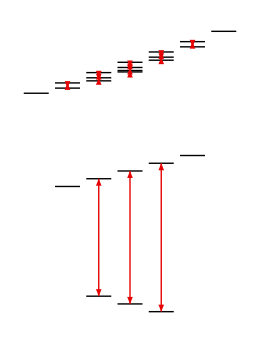

```mathematica
LevelDiagram[,h/.Energy[2]->5/.atomicData/.{Mega-> 10^-4,Second->1,ΩL->0.5}]
```

Now we write the various input parameters in terms of experimentally relevant quantities.

ExpandDipoleRME expresses the reduced dipole matrix element in terms of the natural width and energy of the transition.

```mathematica
dADM=ExpandDipoleRME[system,ReducedME[1,{Dipole,1},2]]
```

√3 √(NaturalWidth[2]/Energy[2]^3)

Convert ADM units to cgs by multiplying by √(ℏ c^3), and then to SI by multiplying by √(4 π ϵ_0).

```mathematica
dSI=Convert[dADM √(ℏ c^3)√(4 π ϵ0)/.atomicData,Coulomb Meter]
```

5.06889×10^-29 Coulomb Meter

Write the optical electric field (in V/m)  in terms of the light intensity (in mW/cm^2).

```mathematica
E0=Convert[√(2Int(Milli Watt/Centimeter^2)/(c ϵ0))/.atomicData//N,Volt/Meter]
```

(86.8021 √Int Volt)/Meter

Write the Rabi frequency in terms of the light intensity.

```mathematica
rabi=ΩR->Convert[E0 dSI/ℏ/.atomicData,1/Second]
```

ΩR→(4.17222×10^7 √Int)/Second

Write the Larmor frequency in terms of the magnetic field in Gauss.

```mathematica
larmor=ΩL->Convert[b Gauss BohrMagneton/ℏ/.atomicData,1/Second]
```

ΩL→(8.79411×10^6 b)/Second

```mathematica
MatrixForm/@({energies,states}=Chop[Eigensystem[h/.larmor/.atomicData/.Mega->10^6/.Second->1/.b->0],10^-9])
```

{(2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
2.41419×10^15
-2.68397×10^10
-2.68397×10^10
-2.68397×10^10
1.61038×10^10
1.61038×10^10
1.61038×10^10
1.61038×10^10
1.61038×10^10),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

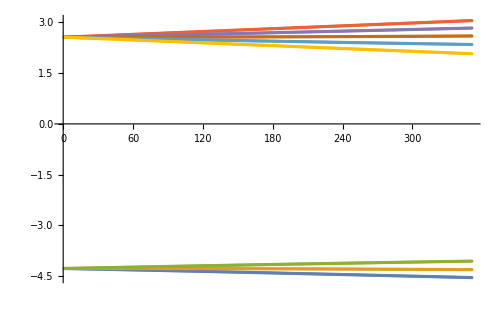

```mathematica
ListPlot[groundZeeman=1/(2π)10^-9*Transpose@Table[Eigenvalues[h/.larmor/.atomicData/.Mega->10^6/.Second->1][[-8;;-1]],{b,0,350,1}]]
```

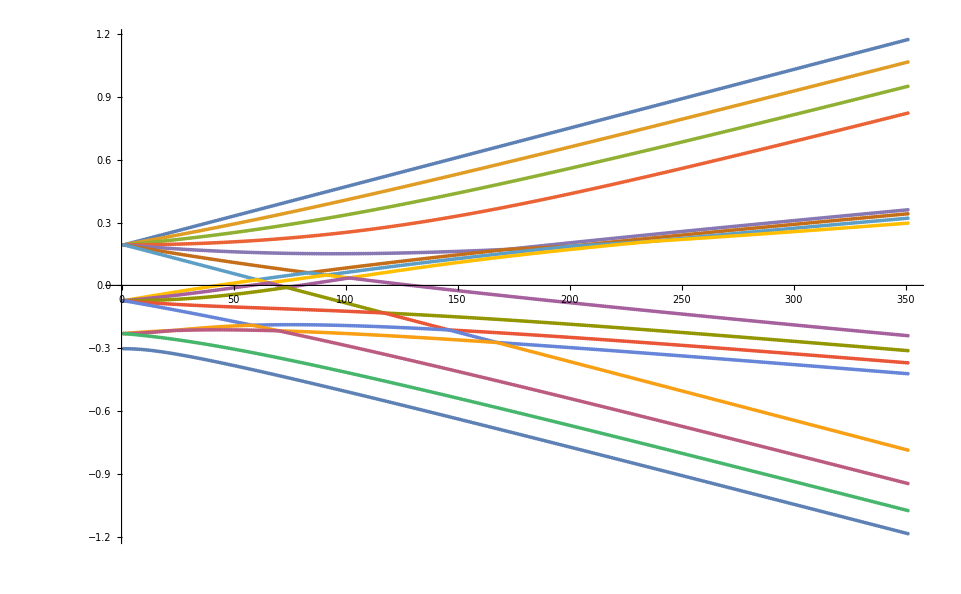

```mathematica
ListPlot[excitedZeeman=-(1/(2π)10^-9 Energy[2]/.atomicData/.Mega->10^6/.Second->1)+1/(2π)10^-9 Transpose@Table[Eigenvalues[h/.larmor/.atomicData/.Mega->10^6/.Second->1][[1;;16]],{b,0,350,1}]]
```

```mathematica
excitedZeeman[[2]]-groundZeeman[[5]]
```

{-14.8865,-14.8792,-14.8718,-14.8644,-14.8569,-14.8494,-14.8419,-14.8343,-14.8267,-14.819,-14.8113,-14.8036,-14.7958,-14.788,-14.7802,-14.7723,-14.7644,-14.7564,-14.7484,-14.7404,-14.7323,-14.7242,-14.7161,-14.7079,-14.6997,-14.6914,-14.6831,-14.6748,-14.6665,-14.6581,-14.6496,-14.6412,-14.6326,-14.6241,-14.6155,-14.6069,-14.5983,-14.5896,-14.5809,-14.5721,-14.5633,-14.5545,-14.5457,-14.5368,-14.5279,-14.5189,-14.5099,-14.5009,-14.4918,-14.4828,-14.4736,-14.4645,-14.4553,-14.4461,-14.4369,-14.4276,-14.4183,-14.409,-14.3996,-14.3902,-14.3808,-14.3713,-14.3618,-14.3523,-14.3428,-14.3332,-14.3236,-14.314,-14.3043,-14.2947,-14.2849,-14.2752,-14.2654,-14.2557,-14.2458,-14.236,-14.2261,-14.2162,-14.2063,-14.1964,-14.1864,-14.1764,-14.1664,-14.1563,-14.1463,-14.1362,-14.1261,-14.1159,-14.1058,-14.0956,-14.0854,-14.0752,-14.0649,-14.0546,-14.0443,-14.034,-14.0237,-14.0133,-14.003,-13.9926,-13.9821,-13.9717,-13.9613,-13.9508,-13.9403,-13.9298,-13.9192,-13.9087,-13.8981,-13.8875,-13.8769,-13.8663,-13.8556,-13.845,-13.8343,-13.8236,-13.8129,-13.8022,-13.7914,-13.7806,-13.7699,-13.7591,-13.7483,-13.7374,-13.7266,-13.7157,-13.7049,-13.694,-13.6831,-13.6722,-13.6612,-13.6503,-13.6393,-13.6284,-13.6174,-13.6064,-13.5954,-13.5843,-13.5733,-13.5623,-13.5512,-13.5401,-13.529,-13.5179,-13.5068,-13.4957,-13.4846,-13.4734,-13.4622,-13.4511,-13.4399,-13.4287,-13.4175,-13.4063,-13.3951,-13.3838,-13.3726,-13.3613,-13.3501,-13.3388,-13.3275,-13.3162,-13.3049,-13.2936,-13.2823,-13.2709,-13.2596,-13.2482,-13.2369,-13.2255,-13.2141,-13.2028,-13.1914,-13.18,-13.1686,-13.1571,-13.1457,-13.1343,-13.1228,-13.1114,-13.0999,-13.0885,-13.077,-13.0655,-13.054,-13.0425,-13.031,-13.0195,-13.008,-12.9965,-12.985,-12.9734,-12.9619,-12.9503,-12.9388,-12.9272,-12.9157,-12.9041,-12.8925,-12.8809,-12.8693,-12.8578,-12.8462,-12.8346,-12.8229,-12.8113,-12.7997,-12.7881,-12.7764,-12.7648,-12.7532,-12.7415,-12.7299,-12.7182,-12.7066,-12.6949,-12.6832,-12.6715,-12.6599,-12.6482,-12.6365,-12.6248,-12.6131,-12.6014,-12.5897,-12.578,-12.5663,-12.5546,-12.5428,-12.5311,-12.5194,-12.5076,-12.4959,-12.4842,-12.4724,-12.4607,-12.4489,-12.4372,-12.4254,-12.4137,-12.4019,-12.3901,-12.3784,-12.3666,-12.3548,-12.343,-12.3313,-12.3195,-12.3077,-12.2959,-12.2841,-12.2723,-12.2605,-12.2487,-12.2369,-12.2251,-12.2133,-12.2015,-12.1897,-12.1779,-12.166,-12.1542,-12.1424,-12.1306,-12.1187,-12.1069,-12.0951,-12.0833,-12.0714,-12.0596,-12.0477,-12.0359,-12.0241,-12.0122,-12.0004,-11.9885,-11.9767,-11.9648,-11.953,-11.9411,-11.9293,-11.9174,-11.9055,-11.8937,-11.8818,-11.8699,-11.8581,-11.8462,-11.8343,-11.8225,-11.8106,-11.7987,-11.7869,-11.775,-11.7631,-11.7512,-11.7394,-11.7275,-11.7156,-11.7037,-11.6918,-11.6799,-11.6681,-11.6562,-11.6443,-11.6324,-11.6205,-11.6086,-11.5967,-11.5848,-11.5729,-11.561,-11.5492,-11.5373,-11.5254,-11.5135,-11.5016,-11.4897,-11.4778,-11.4659,-11.454,-11.4421,-11.4302,-11.4183,-11.4064,-11.3945,-11.3826,-11.3707,-11.3588,-11.3469,-11.335,-11.323,-11.3111,-11.2992,-11.2873,-11.2754,-11.2635,-11.2516,-11.2397,-11.2278,-11.2159,-11.204,-11.1921,-11.1802,-11.1683,-11.1563,-11.1444,-11.1325,-11.1206,-11.1087,-11.0968}

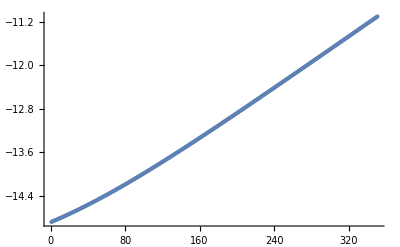

```mathematica
ListPlot[excitedZeeman[[2]]-groundZeeman[[5]]]
```

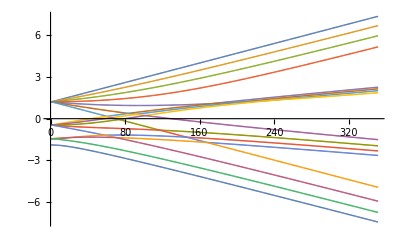

```mathematica
ListPlot[excitedZeeman[[1;;16]]]
```

```mathematica
states.(DipoleOriginal[[1,3]]/ΩR).Transpose[states]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00902032 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00382084 | 0. | 0. | 0. | -0.0111822 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0541879 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0207607 | 0. | 0. | 0. | -0.0674614 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0344932 | 0. | 0. | 0. | -0.0636425 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.181791 | 0. | 0. | 0. | 0.237628 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.108874 | 0. | 0. | 0. | -0.268881 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0603171 | 0. | 0. | 0. | -0.279471 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.2834 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.319195 | 0. | 0. | 0. | -0.37674 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.406753 | 0. | 0. | 0. | -0.280169 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.460736 | 0. | 0. | 0. | -0.184911 | 0. | 0. | 0.
0. | -0.170755 | 0. | 0. | -0.296336 | -3.75004×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.263967 | 0. | 0. | -0.28807 | 0. | 0. | 0. | 0. | 0. | 0.0466791 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.364059 | 0. | 0. | 0.252155 | 0. | 0. | 0. | -0.04769 | 0. | 0. | 0. | 0. | 0.00209964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.463315 | 0. | 0. | -0.0412327 | 2.46368×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.412414 | 0. | 0. | -0.0867382 | 0. | 0. | 0. | 0. | 0. | 0.0297116 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.327631 | 0. | 0. | 0.157397 | 0. | 0. | 0. | -0.0530024 | 0. | 0. | 0. | 0. | 0.00287052 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.279743 | 0. | 0.0711014 | 0. | 0. | 0. | 0. | -0.00469114 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Style[(DipoleOriginal=WignerEckart[system,{Dipole,1}]//.ReducedME[1,{Dipole,1},2]->ΩR)//MatrixForm,Small]
```

((0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √6) | 0 | 0 | 0 | ΩR/(2 √10) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | ΩR/(4 √5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | ΩR/(4 √15) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √6) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(4 √3) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | ΩR/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √2) | 0 | 0 | 0 | 0
-ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(2 √6) | 0 | 0 | 0 | -ΩR/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/4 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(4 √15) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(4 √5) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | ΩR/(4 √3) | 0 | 0 | 0 | ΩR/(4 √5) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 √(3/5) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √15) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | ΩR/(4 √5) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 √(3/5) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√(2/15) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩR/(4 √3) | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩR/(4 √5) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ΩR/(4 √5) | 0 | 0 | 0 | -1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | ΩR/(4 √15) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | ΩR/(4 √5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √6) | 0 | 0 | 0 | ΩR/(2 √10) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/4 | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ΩR/(4 √3) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | ΩR/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ΩR/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(2 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ΩR/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ΩR/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ΩR/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ΩR/4 | 0 | 0 | 0 | -ΩR/(4 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ΩR/4 | 0 | 0 | 0 | -ΩR/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ΩR/(2 √6) | 0 | 0 | 0 | -ΩR/(2 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ΩR/(2 √10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ΩR/(4 √5) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ΩR/(4 √15) | 0 | 0 | 0 | 1/4 √(5/3) ΩR | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ΩR/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))

```mathematica
MatrixForm[repop=OpticalRepopulation[system]]
```

(1/10 NaturalWidth[2] ρ_(Re,{2,1,1},{2,1,1})+1/6 NaturalWidth[2] ρ_(Re,{2,2,1},{2,2,1})+1/3 NaturalWidth[2] ρ_(Re,{2,2,2},{2,2,2})+1/15 NaturalWidth[2] ρ_(Re,{2,3,1},{2,3,1})+1/3 NaturalWidth[2] ρ_(Re,{2,3,2},{2,3,2})+NaturalWidth[2] ρ_(Re,{2,3,3},{2,3,3}) | (NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0})))/(10 √2)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0})))/(2 √6)+1/6 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,1})+ρ_(Re,{2,2,2},{2,2,1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,0})+ρ_(Re,{2,3,1},{2,3,0})))/(5 √3)+2/3 √(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,1})+ρ_(Re,{2,3,2},{2,3,1}))+√(2/3) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,3},{2,3,2})+ρ_(Re,{2,3,3},{2,3,2})) | (NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1})))/(10 √6)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1})))/(2 √6)+1/5 √(2/3) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,-1})+ρ_(Re,{2,3,1},{2,3,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,0})+ρ_(Re,{2,3,2},{2,3,0})))/(√5)+√(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,3},{2,3,1})+ρ_(Re,{2,3,3},{2,3,1})) | 1/6 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,-2})+ρ_(Re,{2,2,1},{2,2,-2}))-1/6 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,-1})+ρ_(Re,{2,2,2},{2,2,-1}))+1/3 √(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,-2})+ρ_(Re,{2,3,1},{2,3,-2}))+2/3 √(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,-1})+ρ_(Re,{2,3,2},{2,3,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,3},{2,3,0})+ρ_(Re,{2,3,3},{2,3,0})))/(√5) | -1/3 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,-2})+ρ_(Re,{2,2,2},{2,2,-2}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,-3})+ρ_(Re,{2,3,1},{2,3,-3})))/(√15)+1/3 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,-2})+ρ_(Re,{2,3,2},{2,3,-2}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,3},{2,3,-1})+ρ_(Re,{2,3,3},{2,3,-1})))/(√15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0})))/(10 √2)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0})))/(2 √6)+1/6 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,1})+ρ_(Re,{2,2,2},{2,2,1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,0})+ρ_(Re,{2,3,1},{2,3,0})))/(5 √3)+2/3 √(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,1})+ρ_(Re,{2,3,2},{2,3,1}))+√(2/3) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,3},{2,3,2})+ρ_(Re,{2,3,3},{2,3,2})) | 1/20 NaturalWidth[2] ρ_(Re,{2,1,0},{2,1,0})+1/20 NaturalWidth[2] ρ_(Re,{2,1,1},{2,1,1})+1/4 NaturalWidth[2] ρ_(Re,{2,2,0},{2,2,0})+1/12 NaturalWidth[2] ρ_(Re,{2,2,1},{2,2,1})+1/6 NaturalWidth[2] ρ_(Re,{2,2,2},{2,2,2})+1/5 NaturalWidth[2] ρ_(Re,{2,3,0},{2,3,0})+8/15 NaturalWidth[2] ρ_(Re,{2,3,1},{2,3,1})+2/3 NaturalWidth[2] ρ_(Re,{2,3,2},{2,3,2}) | (NaturalWidth[2] (ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1})))/(20 √3)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0})))/(10 √3)+1/4 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,1})+ρ_(Re,{2,2,2},{2,2,1})))/(2 √6)+1/5 √2 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,0},{2,3,-1})+ρ_(Re,{2,3,0},{2,3,-1}))+2/5 √2 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,0})+ρ_(Re,{2,3,1},{2,3,0}))+(2 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,1})+ρ_(Re,{2,3,2},{2,3,1})))/(√15) | 1/20 NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,0},{2,2,-2})+ρ_(Re,{2,2,0},{2,2,-2})))/(2 √6)-1/12 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,0})+ρ_(Re,{2,2,2},{2,2,0})))/(2 √6)+√(2/15) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,0},{2,3,-2})+ρ_(Re,{2,3,0},{2,3,-2}))+8/15 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,-1})+ρ_(Re,{2,3,1},{2,3,-1}))+√(2/15) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,0})+ρ_(Re,{2,3,2},{2,3,0})) | -1/6 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,-2})+ρ_(Re,{2,2,1},{2,2,-2}))+1/6 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,-1})+ρ_(Re,{2,2,2},{2,2,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,0},{2,3,-3})+ρ_(Re,{2,3,0},{2,3,-3})))/(√5)+2/3 √(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,-2})+ρ_(Re,{2,3,1},{2,3,-2}))+1/3 √(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,2},{2,3,-1})+ρ_(Re,{2,3,2},{2,3,-1})) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1})))/(10 √6)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1})))/(2 √6)+1/5 √(2/3) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,-1})+ρ_(Re,{2,3,1},{2,3,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,0})+ρ_(Re,{2,3,2},{2,3,0})))/(√5)+√(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,3},{2,3,1})+ρ_(Re,{2,3,3},{2,3,1})) | (NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1})))/(20 √3)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0})))/(10 √3)+1/4 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,1})+ρ_(Re,{2,2,2},{2,2,1})))/(2 √6)+1/5 √2 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,0},{2,3,-1})+ρ_(Re,{2,3,0},{2,3,-1}))+2/5 √2 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,0})+ρ_(Re,{2,3,1},{2,3,0}))+(2 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,1})+ρ_(Re,{2,3,2},{2,3,1})))/(√15) | 1/60 NaturalWidth[2] ρ_(Re,{2,1,-1},{2,1,-1})+1/15 NaturalWidth[2] ρ_(Re,{2,1,0},{2,1,0})+1/60 NaturalWidth[2] ρ_(Re,{2,1,1},{2,1,1})+1/4 NaturalWidth[2] ρ_(Re,{2,2,-1},{2,2,-1})+1/4 NaturalWidth[2] ρ_(Re,{2,2,1},{2,2,1})+2/5 NaturalWidth[2] ρ_(Re,{2,3,-1},{2,3,-1})+3/5 NaturalWidth[2] ρ_(Re,{2,3,0},{2,3,0})+2/5 NaturalWidth[2] ρ_(Re,{2,3,1},{2,3,1}) | (NaturalWidth[2] (ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1})))/(10 √3)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0})))/(20 √3)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,-1},{2,2,-2})+ρ_(Re,{2,2,-1},{2,2,-2})))/(2 √6)+1/4 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0}))+(2 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,-1},{2,3,-2})+ρ_(Re,{2,3,-1},{2,3,-2})))/(√15)+2/5 √2 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,0},{2,3,-1})+ρ_(Re,{2,3,0},{2,3,-1}))+1/5 √2 NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,0})+ρ_(Re,{2,3,1},{2,3,0})) | (NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1})))/(10 √6)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1})))/(2 √6)+√(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,-1},{2,3,-3})+ρ_(Re,{2,3,-1},{2,3,-3}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,0},{2,3,-2})+ρ_(Re,{2,3,0},{2,3,-2})))/(√5)+1/5 √(2/3) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,1},{2,3,-1})+ρ_(Re,{2,3,1},{2,3,-1})) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,-2})+ρ_(Re,{2,2,1},{2,2,-2}))-1/6 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,-1})+ρ_(Re,{2,2,2},{2,2,-1}))+1/3 √(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,-2})+ρ_(Re,{2,3,1},{2,3,-2}))+2/3 √(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,-1})+ρ_(Re,{2,3,2},{2,3,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,3},{2,3,0})+ρ_(Re,{2,3,3},{2,3,0})))/(√5) | 1/20 NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,0},{2,2,-2})+ρ_(Re,{2,2,0},{2,2,-2})))/(2 √6)-1/12 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,0})+ρ_(Re,{2,2,2},{2,2,0})))/(2 √6)+√(2/15) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,0},{2,3,-2})+ρ_(Re,{2,3,0},{2,3,-2}))+8/15 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,-1})+ρ_(Re,{2,3,1},{2,3,-1}))+√(2/15) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,0})+ρ_(Re,{2,3,2},{2,3,0})) | (NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1})))/(10 √3)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0})))/(20 √3)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,-1},{2,2,-2})+ρ_(Re,{2,2,-1},{2,2,-2})))/(2 √6)+1/4 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0}))+(2 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,-1},{2,3,-2})+ρ_(Re,{2,3,-1},{2,3,-2})))/(√15)+2/5 √2 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,0},{2,3,-1})+ρ_(Re,{2,3,0},{2,3,-1}))+1/5 √2 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,0})+ρ_(Re,{2,3,1},{2,3,0})) | 1/20 NaturalWidth[2] ρ_(Re,{2,1,-1},{2,1,-1})+1/20 NaturalWidth[2] ρ_(Re,{2,1,0},{2,1,0})+1/6 NaturalWidth[2] ρ_(Re,{2,2,-2},{2,2,-2})+1/12 NaturalWidth[2] ρ_(Re,{2,2,-1},{2,2,-1})+1/4 NaturalWidth[2] ρ_(Re,{2,2,0},{2,2,0})+2/3 NaturalWidth[2] ρ_(Re,{2,3,-2},{2,3,-2})+8/15 NaturalWidth[2] ρ_(Re,{2,3,-1},{2,3,-1})+1/5 NaturalWidth[2] ρ_(Re,{2,3,0},{2,3,0}) | (NaturalWidth[2] (ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1})))/(10 √2)+1/6 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,-1},{2,2,-2})+ρ_(Re,{2,2,-1},{2,2,-2}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1})))/(2 √6)+√(2/3) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,-2},{2,3,-3})+ρ_(Re,{2,3,-2},{2,3,-3}))+2/3 √(2/5) NaturalWidth[2] (ⅈ ρ_(Im,{2,3,-1},{2,3,-2})+ρ_(Re,{2,3,-1},{2,3,-2}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,3,0},{2,3,-1})+ρ_(Re,{2,3,0},{2,3,-1})))/(5 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/3 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,-2})+ρ_(Re,{2,2,2},{2,2,-2}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,-3})+ρ_(Re,{2,3,1},{2,3,-3})))/(√15)+1/3 NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,-2})+ρ_(Re,{2,3,2},{2,3,-2}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,3},{2,3,-1})+ρ_(Re,{2,3,3},{2,3,-1})))/(√15) | -1/6 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,-2})+ρ_(Re,{2,2,1},{2,2,-2}))+1/6 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,-1})+ρ_(Re,{2,2,2},{2,2,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,0},{2,3,-3})+ρ_(Re,{2,3,0},{2,3,-3})))/(√5)+2/3 √(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,-2})+ρ_(Re,{2,3,1},{2,3,-2}))+1/3 √(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,2},{2,3,-1})+ρ_(Re,{2,3,2},{2,3,-1})) | (NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1})))/(10 √6)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1})))/(2 √6)+√(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,-1},{2,3,-3})+ρ_(Re,{2,3,-1},{2,3,-3}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,0},{2,3,-2})+ρ_(Re,{2,3,0},{2,3,-2})))/(√5)+1/5 √(2/3) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,1},{2,3,-1})+ρ_(Re,{2,3,1},{2,3,-1})) | (NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1})))/(10 √2)+1/6 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,-1},{2,2,-2})+ρ_(Re,{2,2,-1},{2,2,-2}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1})))/(2 √6)+√(2/3) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,-2},{2,3,-3})+ρ_(Re,{2,3,-2},{2,3,-3}))+2/3 √(2/5) NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,-1},{2,3,-2})+ρ_(Re,{2,3,-1},{2,3,-2}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,3,0},{2,3,-1})+ρ_(Re,{2,3,0},{2,3,-1})))/(5 √3) | 1/10 NaturalWidth[2] ρ_(Re,{2,1,-1},{2,1,-1})+1/3 NaturalWidth[2] ρ_(Re,{2,2,-2},{2,2,-2})+1/6 NaturalWidth[2] ρ_(Re,{2,2,-1},{2,2,-1})+NaturalWidth[2] ρ_(Re,{2,3,-3},{2,3,-3})+1/3 NaturalWidth[2] ρ_(Re,{2,3,-2},{2,3,-2})+1/15 NaturalWidth[2] ρ_(Re,{2,3,-1},{2,3,-1}) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 NaturalWidth[2] ρ_(Re,{2,0,0},{2,0,0})+5/12 NaturalWidth[2] ρ_(Re,{2,1,0},{2,1,0})+5/12 NaturalWidth[2] ρ_(Re,{2,1,1},{2,1,1})+1/12 NaturalWidth[2] ρ_(Re,{2,2,0},{2,2,0})+1/4 NaturalWidth[2] ρ_(Re,{2,2,1},{2,2,1})+1/2 NaturalWidth[2] ρ_(Re,{2,2,2},{2,2,2}) | 5/12 NaturalWidth[2] (ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1})))/(4 √3)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0})))/(2 √3)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,1})+ρ_(Re,{2,2,2},{2,2,1})))/(2 √2) | -5/12 NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,0},{2,2,-2})+ρ_(Re,{2,2,0},{2,2,-2})))/(2 √6)+1/4 NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,2},{2,2,0})+ρ_(Re,{2,2,2},{2,2,0})))/(2 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5/12 NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,0},{2,1,-1})+ρ_(Re,{2,1,0},{2,1,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1})))/(4 √3)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0})))/(2 √3)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,1})+ρ_(Re,{2,2,2},{2,2,1})))/(2 √2) | 1/3 NaturalWidth[2] ρ_(Re,{2,0,0},{2,0,0})+5/12 NaturalWidth[2] ρ_(Re,{2,1,-1},{2,1,-1})+5/12 NaturalWidth[2] ρ_(Re,{2,1,1},{2,1,1})+1/4 NaturalWidth[2] ρ_(Re,{2,2,-1},{2,2,-1})+1/3 NaturalWidth[2] ρ_(Re,{2,2,0},{2,2,0})+1/4 NaturalWidth[2] ρ_(Re,{2,2,1},{2,2,1}) | 5/12 NaturalWidth[2] (ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0}))+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,-1},{2,2,-2})+ρ_(Re,{2,2,-1},{2,2,-2})))/(2 √2)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1})))/(2 √3)+(NaturalWidth[2] (ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0})))/(4 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5/12 NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,-1})+ρ_(Re,{2,1,1},{2,1,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,0},{2,2,-2})+ρ_(Re,{2,2,0},{2,2,-2})))/(2 √6)+1/4 NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,-1})+ρ_(Re,{2,2,1},{2,2,-1}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,2},{2,2,0})+ρ_(Re,{2,2,2},{2,2,0})))/(2 √6) | 5/12 NaturalWidth[2] (-ⅈ ρ_(Im,{2,1,1},{2,1,0})+ρ_(Re,{2,1,1},{2,1,0}))+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,-1},{2,2,-2})+ρ_(Re,{2,2,-1},{2,2,-2})))/(2 √2)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,0},{2,2,-1})+ρ_(Re,{2,2,0},{2,2,-1})))/(2 √3)+(NaturalWidth[2] (-ⅈ ρ_(Im,{2,2,1},{2,2,0})+ρ_(Re,{2,2,1},{2,2,0})))/(4 √3) | 1/3 NaturalWidth[2] ρ_(Re,{2,0,0},{2,0,0})+5/12 NaturalWidth[2] ρ_(Re,{2,1,-1},{2,1,-1})+5/12 NaturalWidth[2] ρ_(Re,{2,1,0},{2,1,0})+1/2 NaturalWidth[2] ρ_(Re,{2,2,-2},{2,2,-2})+1/4 NaturalWidth[2] ρ_(Re,{2,2,-1},{2,2,-1})+1/12 NaturalWidth[2] ρ_(Re,{2,2,0},{2,2,0}) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)